## DEFINE PARAMETERS

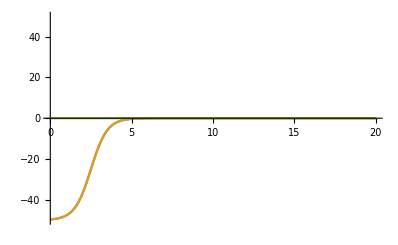

```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=50;R=2.5;a=0.5;μ=8/9 Subscript[m, N];l=0;
rmax=20.;dr=0.02;
rlist=Range[dr,rmax,dr];
len=Length[rlist];
Vwoods[r_]:=-V0/(1+Exp[(r-R)/a]);
Vcent[r_]:=(l(l+1)ℏc^2)/(2μ r^2);
V[r_]:=-V0/(1+Exp[(r-R)/a])+(l(l+1)ℏc^2)/(2μ r^2);
Vmat=DiagonalMatrix[V[rlist]];
ListLinePlot[{V[rlist],Vwoods[rlist],Vcent[rlist]},DataRange->{dr,rmax},PlotRange->{-V0,V0}]
```

```mathematica
(*INITIAL HAMILTONIAN*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
H0:=Vmat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1]);
```

## BOUND SOLUTIONS

```mathematica
(*BOUND SOLUTION*)
κ[En_]:=Sqrt[(2μ En)/ℏc^2];
wavebound[En_,r_,l_]:=r SphericalHankelH1[l,κ[En] r];
Bbound[En_,l_]:=rmax/wavebound[En,rmax,l](D[wavebound[En,r,l],r]/.r->rmax);
(*HAMILTONIAN*)
Hnewbound[En_,l_]:=(H=H0;H[[len,len]]=Vmat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bbound[En,l]/rmax-1);H);
(*RETURNS EIGENVALUE*)
eigenvbound[{En_,i_,l_}]:=({evalbound,evecbound}=Transpose@SortBy[Transpose[Eigensystem[Hnewbound[En,l]]],First];{evalbound[[i]],i,l})
```

```mathematica
ϵ=10^-10;
n=1;
evalsbound=List[];evecsbound=List[];
```

```mathematica
(*RETURNS EIGENSYSTEM*)
En=NestWhileList[eigenvbound,{-V0/2,n,l},Abs[#1[[1]]-#2[[1]]]>ϵ&,2,100][[-1,1]];
While[Re[En]<0,
evalsbound=Append[evalsbound,En];
evecsbound=Append[evecsbound,evecbound[[n]]];n++;En=NestWhileList[eigenvbound,{-V0/2,n,l},Abs[#1[[1]]-#2[[1]]]>ϵ&,2,100][[-1,1]];]
```

```mathematica
evalsbound
```

{-23.0975+0. ⅈ,-0.57457-0.684651 ⅈ}

```mathematica
evalsbound(*rmax=10fm,V0=9MeV,dr=0.01*)
```

{}

```mathematica
evalsbound(*rmax=10fm,V0=8MeV,dr=0.01*)
```

{}

```mathematica
evalsbound(*rmax=20fm,V0=9MeV,dr=0.01fm*)
```

{-0.00758694+0. ⅈ}

```mathematica
evalsbound(*rmax=20fm,V0=9MeV,dr=0.02fm*)
```

{-0.00759041+0. ⅈ}

```mathematica
evalsbound(*rmax=20fm,V0=8MeV,dr=0.02fm*)
```

{}

```mathematica
(*MATCHES AMPLITUDE & PLOTS*)
constbound[i_]:=evecsbound[[i,-1]]/Abs[wavebound[evalsbound[[i]],rmax,l]];
rmaxx=25.;
normbound[i_]:=Module[{ψ=Interpolation[Transpose[{Flatten[Append[rlist,Range[rmax+dr,rmaxx,dr]]],Flatten[Append[evecsbound⟦i⟧,constbound[i] wavebound[evalsbound[[i]],Range[rmax+dr,rmaxx,dr],l]]]}]]},Sqrt[1/NIntegrate[Abs[ψ[x]]^2,{x,dr,rmaxx}]]]
Manipulate[ListLinePlot[{Transpose[{rlist,normbound[i] evecsbound⟦i⟧}],Transpose[{Range[rmax,rmaxx,dr],normbound[i]constbound[i]Abs[wavebound[evalsbound[[i]],Range[rmax,rmaxx,dr],l]]}]},PlotRange->All],{i,1,Length[evalsbound],1}]
```

## RESONANCE STATES

```mathematica
(*RESONANCE SOLUTION*)
k[En_?NumericQ]:=Sqrt[(2μ En)/ℏc^2];
waveres[En_?NumericQ,r_,l_]:=SphericalHankelH1[l,k[En] r];
Bres[En_?NumericQ,l_]:=rmax/waveres[En,rmax,l](D[waveres[En,r,l],r]/.r->rmax);
(*HAMILTONIAN*)
Hnewres[En_?NumericQ,l_]:=(H=H0;H[[len,len]]=Vmat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bres[En,l]/rmax-1);H);
(*RETURNS EIGENVALUE*)
eigenvres[{En_?NumericQ,i_,l_}]:=({evalres,evecres}=Transpose@SortBy[Transpose[Eigensystem[Hnewres[En,l]]],First];{evalres[[i]],i,l})
(*eigenvres1[En_?NumericQ,i_,l_]:=({eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnewres[En,l]]],First];eval[[i]])*)
```

```mathematica
ϵ=10^-10;
n=1;
evalsres=List[];evecsres=List[];
```

```mathematica
(*RETURNS EIGENSYSTEM*)
(*En=x/.FindRoot[Im[eigenvres1[x,n,l]]==Im[x],{x,0.1+0.I,0.,V0}]//Timing*)
En=NestWhileList[eigenvres,{0,n,l},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,100][[-1,1]];
evalsres=Append[evalsres,En];evecsres=Append[evecsres,evecres[[n]]];
```

```mathematica
evalsres(*V0=8MeV,rmax=10fm,dr=0.01fm*)
```

{0.238353-0.216854 ⅈ}

```mathematica
evalsres(*V0=8MeV,rmax=20fm,dr=0.02fm*)
```

{0.0659602-0.0495609 ⅈ}

```mathematica
(*For[i=2,i≤5,i++,En=NestWhileList[eigenvres,{0,i,l},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,100][[-1,1]];
evalsres=Append[evalsres,En];
evecsres=Append[evecsres,evecres[[i]]];]*)
```

```mathematica
(*MATCHES AMPLITUDE & PLOTS*)
constres[i_]:=evecsres[[i,-1]]/waveres[evalsres[[i]],rmax,l];
rmaxx=50.;
```

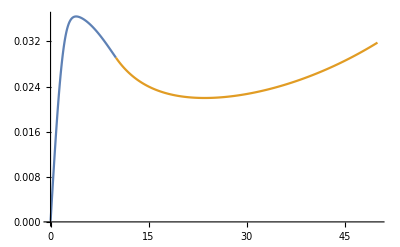

```mathematica
ListLinePlot[{Transpose[{rlist,Abs[evecsres⟦1⟧]}],Transpose[{Range[rmax,rmaxx,dr],Abs[constres[1] waveres[evalsres[[1]],Range[rmax,rmaxx,dr],l]]}]},PlotRange->All](*V0=8MeV,rmax=10fm,dr=0.01fm*)
```

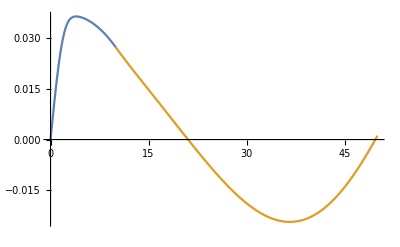

```mathematica
ListLinePlot[{Transpose[{rlist,Re[evecsres⟦1⟧]}],Transpose[{Range[rmax,rmaxx,dr],Re[constres[1] waveres[evalsres[[1]],Range[rmax,rmaxx,dr],l]]}]},PlotRange->All](*V0=8MeV,rmax=10fm,dr=0.01fm.....this grows exponentially with sinusoidal variation*)
```

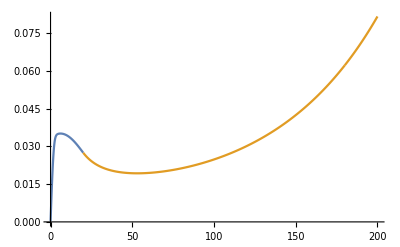

```mathematica
ListLinePlot[{Transpose[{rlist,Abs[evecsres⟦1⟧]}],Transpose[{Range[rmax,rmaxx,dr],Abs[constres[1] waveres[evalsres[[1]],Range[rmax,rmaxx,dr],l]]}]},PlotRange->All](*V0=8MeV,rmax=20fm,dr=0.02fm*)
```

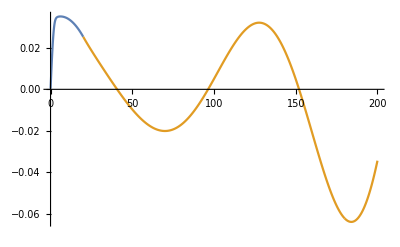

```mathematica
ListLinePlot[{Transpose[{rlist,Re[evecsres⟦1⟧]}],Transpose[{Range[rmax,rmaxx,dr],Re[constres[1] waveres[evalsres[[1]],Range[rmax,rmaxx,dr],l]]}]},PlotRange->All](*V0=8MeV,rmax=20fm,dr=0.02fm.....this grows exponentially with sinusoidal variation*)
```

## SCATTERING SOLUTIONS

```mathematica
(*SCATTERING SOLUTION*)
ks[En_?NumericQ]:=Sqrt[(2μ En)/ℏc^2];
wavescat[En_,r_,δ_,l_]:=1/2 Exp[I δ](Cos[δ]SphericalBesselJ[l,ks[En] r]-Sin[δ] SphericalBesselY[l,ks[En] r]);
(*Bscat[En_?NumericQ,δ_?NumericQ,l_]:=k[En] rmax(((Cos[δ] ∂_x SphericalBesselJ[l,x]/.x->k[En] rmax)-(Sin[δ] ∂_x SphericalBesselY[l,x]/.x->k[En] rmax))/(Cos[δ]SphericalBesselJ[l,k[En] rmax]-Sin[δ]SphericalBesselY[l,k[En] rmax]));*)
Bscat[En_?NumericQ,δ_?NumericQ,l_]:=rmax/wavescat[En,rmax,δ,l] D[wavescat[En,r,δ,l],r]/.{r->rmax};
(*HAMILTONIAN*)
Hnewscat[En_?NumericQ,δ_?NumericQ,l_]:=(H=H0;H[[len,len]]=Vmat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bscat[En,δ,l]/rmax-1);H);
(*RETURNS EIGEINVALUE*)
eigenvscat[En_?NumericQ,i_,δ_?NumericQ,l_]:=({evalscat,evecscat}=Transpose@SortBy[Transpose[Eigensystem[Hnewscat[En,δ,l]]],First];evalscat[[i]]);
(*FINDS ENERGY LEVEL AND PHASE*)
(*findnd[En_]:=Module[{phase=List[],n=1},(While[Max[Table[eigenvscat[{En,n,δ,l}][[1]],{δ,0.,π,0.01}]]<En,n++;];phase=Table[{eigenvscat[{En,n,δ,l}][[1]],δ},{δ,0,π,0.001}];δ=phase[[Position[phase[[All,1]],Nearest[phase[[All,1]],En][[1]]][[1,1]],2]];{n,δ})]*)
findnd[En_?NumericQ]:=Module[{n=1},While[Max[Table[eigenvscat[En,n,x,l],{x,0.,π,0.1}]]<En,n++;];δ=x/.FindRoot[eigenvscat[En,n,x,l]==En,{x,0.,-Pi,Pi}];If[δ<0,δ=π+δ];{n,δ}];
(*MATCHES AMPLITUDE*)
constscat[i_]:=evecscat[[i,-1]]/wavescat[evalscat[[i]],rmax,δ,l];
```

## PLOTS

{0.238535+0. ⅈ,1,0.456772+0. ⅈ}

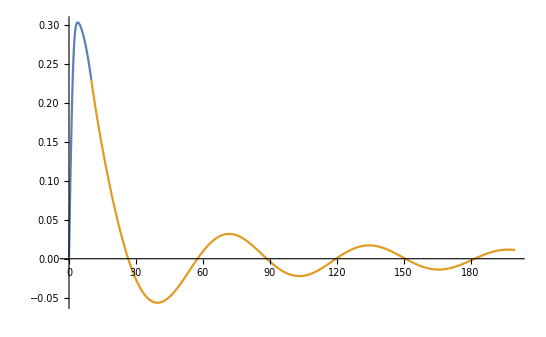

```mathematica
(*V0=10MeV,rmax=10fm,dr=0.01*)
rmaxx=200;
nd=findnd[0.238535];
Print[{evalscat[[n]],n,δ}];
ListLinePlot[{Transpose[{rlist,normscat[nd[[1]]] Re[evecscat⟦nd[[1]]⟧]}],Transpose[{Range[rmax,rmaxx,dr],normscat[nd[[1]]] Re[constscat[nd[[1]]] wavescat[evalscat[[nd[[1]]]],Range[rmax,rmaxx,dr],nd[[2]],l]]}]},PlotRange->All]
```

```mathematica
phasedata=Table[{x,findnd[x][[2]]},{x,0.9,2.0,0.1}];
```

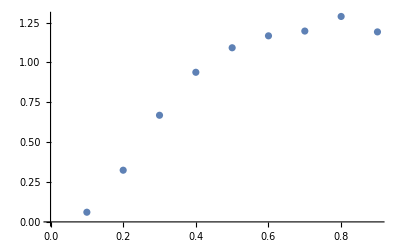

```mathematica
ListPlot[phasedata,GridLines->{None, {{Pi/2,Red}}}]
```

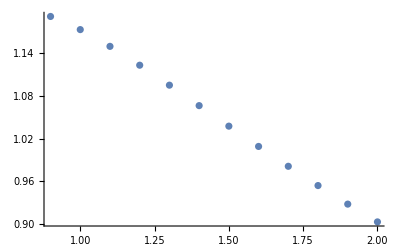

```mathematica
ListPlot[phasedata,GridLines->{None, {{Pi/2,Red}}}]
```

{0.0659602+0. ⅈ,1,0.492893+0. ⅈ}

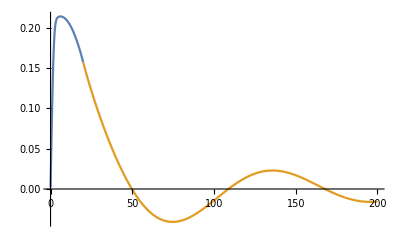

```mathematica
(*V0=10MeV,rmax=20fm,dr=0.02*)
rmaxx=200;
nd=findnd[0.0659602];
Print[{evalscat[[n]],n,δ}];
ListLinePlot[{Transpose[{rlist,normscat[nd[[1]]] Re[evecscat⟦nd[[1]]⟧]}],Transpose[{Range[rmax,rmaxx,dr],normscat[nd[[1]]] Re[constscat[nd[[1]]] wavescat[evalscat[[nd[[1]]]],Range[rmax,rmaxx,dr],nd[[2]],l]]}]},PlotRange->All]
```

```mathematica
phasedata=Table[{x,findnd[x][[2]]},{x,0.1,2.0,0.1}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

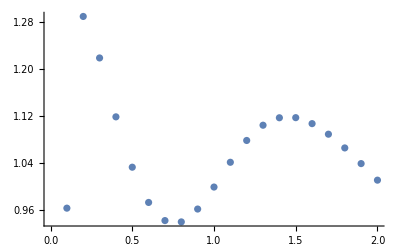

```mathematica
ListPlot[phasedata,GridLines->{None, {{Pi/2,Red}}}]
```